```mathematica
sound=Import["D:\\BaiduNetdiskDownload\\Canon_in_D.mid","SoundNotes"];
sound=sound[[2]];
```

```mathematica
seven="C,C#,D,D#,E,F,F#,G,G#,A,A#,B";
twelve=Range[0,11];
rule=MapThread[Rule,{StringSplit[seven,","],twelve}]
```

{C→0,C#→1,D→2,D#→3,E→4,F→5,F#→6,G→7,G#→8,A→9,A#→10,B→11}

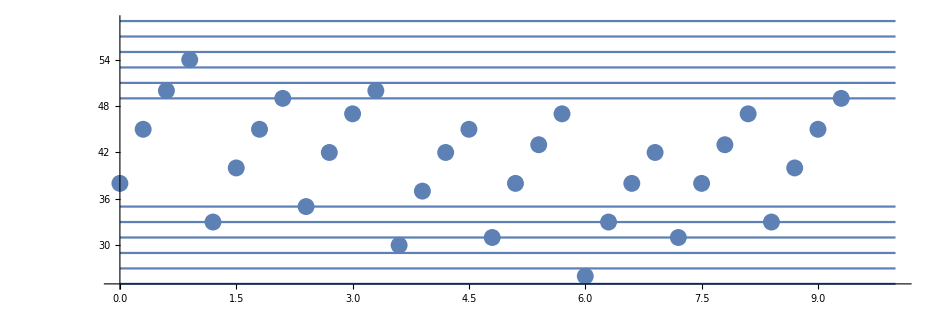

```mathematica
a=({#2[[1]],(StringDrop[#1,-1]/.rule)+12*ToExpression[StringTake [#1,-1]]}&)@@@sound[[1;;32]]//ListPlot;
b=Plot[Table[Range[12*k+1,12*(k+1),2],{k,2,5,2}],{x,0,10},AspectRatio->1/3];

c=({#2[[1]]-9.299984500000003,-24+(StringDrop[#1,-1]/.rule)+12*ToExpression[StringTake [#1,-1]]}&)@@@sound[[33;;67]]//ListPlot;

Show[{b,a}]
```

```mathematica
.
```

```mathematica
First/@sound[[1;;10]]
```

{D3,A3,D4,F#4,A2,E3,A3,C#4,B2,F#3}